v2: updated version following notes, plus Mean-field

### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];DFermi[β_,x_] :=D[ Fermi[β,x1],x1]/.{x1-> x};
```

### Bloch Hamiltonian

```mathematica
MatX[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δx)(IdentityMatrix[2]+ I λR PauliMatrix[2] +I λD PauliMatrix[1]) + (1-δx)Exp[I k.a1](IdentityMatrix[2]- I λR PauliMatrix[2] -I λD PauliMatrix[1])];
```

```mathematica
MatY[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δy)(IdentityMatrix[2]- I λR PauliMatrix[1] +I λD PauliMatrix[2]) + (1-δy)Exp[I k.a2](IdentityMatrix[2]+ I λR PauliMatrix[1] -I λD PauliMatrix[2])];
```

```mathematica
Clear[hamLieb];hamLieb[λ_,δ_,ϵ_,k_] := hamLieb[λ,δ,ϵ,k] = Module[ {mx = MatX[λ,δ,k],my = MatY[λ,δ,k] },ArrayFlatten[ {{-ϵ IdentityMatrix[2],mx,my},{mx†,0,0},{my†,0,0}} ]];
```

```mathematica
Block[ {λ=RandomReal[{0,1},2],δ=RandomReal[1,2],k=RandomReal[2π,2],ϵ=0.1},hamLieb[λ,δ,ϵ,k]]//MatrixForm
```

(-0.1 | 0. | 1.86216-0.26212 ⅈ | 0.412589+0.359511 ⅈ | 1.53537-0.651202 ⅈ | 0.402075-0.213038 ⅈ
0. | -0.1 | -0.509992+0.198459 ⅈ | 1.86216-0.26212 ⅈ | -0.00196302-0.455023 ⅈ | 1.53537-0.651202 ⅈ
1.86216+0.26212 ⅈ | -0.509992-0.198459 ⅈ | 0 | 0 | 0 | 0
0.412589-0.359511 ⅈ | 1.86216+0.26212 ⅈ | 0 | 0 | 0 | 0
1.53537+0.651202 ⅈ | -0.00196302+0.455023 ⅈ | 0 | 0 | 0 | 0
0.402075+0.213038 ⅈ | 1.53537+0.651202 ⅈ | 0 | 0 | 0 | 0)

```mathematica
Clear[EnerLieb];EnerLieb[λ_,δ_,ϵ_,k_] := EnerLieb[λ,δ,ϵ,k]= Chop[  N[Sort[Eigenvalues[hamLieb[λ,δ,ϵ,k] ]]] ];
Clear[ULieb];ULieb[λ_,δ_,ϵ_,k_] :=ULieb[λ,δ,ϵ,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLieb[λ,δ,ϵ,k] ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Block[ {λ=RandomReal[{0,1},2],δ=RandomReal[1,2],k=RandomReal[2π,2],ϵ=0.1},ULieb[λ,δ,ϵ,k]]//MatrixForm
```

(0.271621+0.424866 ⅈ | -0.449145-0.230736 ⅈ | 0 | 0 | 0.440302+0.226193 ⅈ | 0.267+0.417638 ⅈ
-0.467337-0.189436 ⅈ | -0.499842+0.07161 ⅈ | 0 | 0 | 0.490001-0.0702001 ⅈ | -0.459386-0.186213 ⅈ
-0.296655-0.320467 ⅈ | 0.162399+0.116628 ⅈ | -0.609135-0.210144 ⅈ | 0.208536+0.26771 ⅈ | 0.165661+0.11897 ⅈ | 0.301789+0.326013 ⅈ
0.204015-0.0222676 ⅈ | 0.488561-0.0168367 ⅈ | -0.184199+0.242817 ⅈ | -0.576558+0.0365993 ⅈ | 0.498373-0.0171748 ⅈ | -0.207546+0.022653 ⅈ
-0.288577-0.133219 ⅈ | 0.303591+0.226399 ⅈ | 0.701054+0.0206638 ⅈ | 0.0977804-0.0170986 ⅈ | 0.309689+0.230946 ⅈ | 0.293572+0.135525 ⅈ
0.396959 | 0.260162 | 0 | 0.735684 | 0.265387 | -0.403829)

#### Plot Band Structure

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[λ_,δ_,ϵ_] := Table[ EnerLieb[λ,δ,ϵ,k]  ,{k,kCut} ];
```

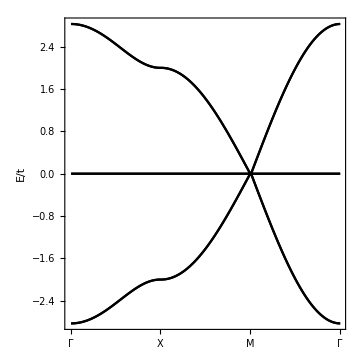

```mathematica
Block[ {λ={0.0,0.0},δ={0.0,0.0},ϵ=0},ListPlot[Table[ PlotDispData[λ,δ,ϵ][[All,i]],{i,1,6}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean Field Theory

Here nup, ndn, splus and sdown are all 3 vectors (for A, B, C)

Follow Eq. 5 of ref https://arxiv.org/pdf/2110.03813.pdf

```mathematica
Clear[HamMFU];HamMFU[nup_, ndn_, spls_, smns_]:= HamMFU[nup,ndn, spls, smns] = {{ ndn[[1]], - smns[[1]],0,0,0,0},{-spls[[1]], nup[[1]],0,0,0,0},{0,0, ndn[[2]], - smns[[2]],0,0},{0,0,-spls[[2]], nup[[2]],0,0},{0,0,0,0, ndn[[3]], - smns[[3]]},{0,0,0,0,-spls[[3]], nup[[3]]}} ;
```

```mathematica
Clear[HamMFUcl];HamMFUcl[nup_, ndn_, spls_, smns_]:= HamMFUcl[nup,ndn, spls, smns] = KroneckerProduct[ArrayFlatten[ Table[ If[i==j, smns[[i]] spls[[i]] -  nup[[i]] ndn[[i]], 0.0] ,{i,1,3},{j,1,3}]],IdentityMatrix[2]] ;
```

```mathematica
Clear[HamMFull];HamMFull[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,k_,U_]:= HamMFull[λ,δ,ϵ,nup,ndn, spls, smns,k,U]= hamLieb[λ,δ,ϵ,k] +U HamMFU[nup,ndn, spls, smns];
```

```mathematica
Clear[EnerMF];EnerMF[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,k_,U_] := EnerMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U]= Chop[  N[Sort[Eigenvalues[HamMFull[λ,δ,ϵ,nup,ndn, spls, smns,k,U] ]]] ];
```

```mathematica
Clear[ULiebMF];ULiebMF[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,k_,U_] :=ULiebMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[HamMFull[λ,δ,ϵ,nup,ndn, spls, smns,k,U]  ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
xyzar = { {1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
Clear[nupMF];nupMF[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=nupMF[λ,δ,ϵ,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U][[band]] -μ]Module[{um = ULiebMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U],zr = {0,0,0}},Table[ (um†.HamMFU[xyz,zr, zr, zr].um)[[band,band]],{xyz,xyzar}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[ndnMF];ndnMF[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=ndnMF[λ,δ,ϵ,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U][[band]] -μ]Module[{um = ULiebMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U],zr = {0,0,0}},Table[ (um†.HamMFU[zr,xyz, zr, zr].um)[[band,band]],{xyz,xyzar}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[splsMF];splsMF[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=splsMF[λ,δ,ϵ,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U][[band]] -μ]Module[{um = ULiebMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U],zr = {0,0,0}},Table[ (um†.HamMFU[zr,zr,xyz, zr].um)[[band,band]],{xyz,xyzar}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[smnsMF];smnsMF[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=smnsMF[λ,δ,ϵ,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U][[band]] -μ]Module[{um = ULiebMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U],zr = {0,0,0}},Table[ (um†.HamMFU[zr,zr,zr, xyz].um)[[band,band]],{xyz,xyzar}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[NumEq];NumEq[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=NumEq[λ,δ,ϵ,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[λ,δ,ϵ,nup,ndn, spls, smns,k,U][[band]] -μ],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[FindMu];FindMu[λ_,δ_,ϵ_,nup_, ndn_, spls_, smns_,U_,fil_,β_,krange_] :=FindMu[λ,δ,ϵ,nup,ndn, spls, smns,U,fil,β,krange]=μ/.FindRoot[ NumEq[λ,δ,ϵ,nup,ndn, spls, smns,U,μ,β,krange]-fil,{μ,-10,10},Evaluated->False, MaxIterations->20,PrecisionGoal->3];
```

```mathematica
Clear[ItrFnMF];ItrFnMF[λ_,δ_,ϵ_,U_,fil_,β_,krange_]:= ItrFnMF[λ,δ,ϵ,U,fil,β,krange]=  NestList[ {FindMu[λ,δ,ϵ,#[[2]],#[[3]], #[[4]],#[[5]],U,fil,β,krange],nupMF[λ,δ,ϵ,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],ndnMF[λ,δ,ϵ,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange] , splsMF[λ,δ,ϵ,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],smnsMF[λ,δ,ϵ,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange]}&,{U,RandomReal[1,3],RandomReal[1,3],RandomReal[1,3],RandomReal[1,3]},10][[10]];
```

#### Checks

```mathematica
Block[{λ={0,0},δ={0.0,0.0},ϵ=0.1,U=3,fil=3.0, β=N[10^6], krange=30,k=Gama},Module[{itr=ItrFnMF[λ,δ,ϵ,U,fil,β,krange]}, itr]]
```

General::munfl: 6.6113488×10^-3514586 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.16460934×10^-3517711 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.05394659×10^-3526986 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 20 iterations.

{-2.21976×10^-9,{3.+0. ⅈ,3.+0. ⅈ,3.+0. ⅈ},{3.+0. ⅈ,3.+0. ⅈ,3.+0. ⅈ},{-7.51714×10^-20-1.59016×10^-20 ⅈ,0.+0. ⅈ,-2.24068×10^-19-4.06576×10^-21 ⅈ},{-7.51714×10^-20+1.59016×10^-20 ⅈ,0.+0. ⅈ,-2.24068×10^-19+4.06576×10^-21 ⅈ}}

### Renormalized MF dispersion

```mathematica
Clear[MFEn];MFEn[ λ_,δ_,ϵ_,U_,fil_,β_,k_,krange_]:= MFEn[λ,δ,ϵ,U,fil,β,k,krange]= Module[{itr=ItrFnMF[λ,δ,ϵ,U,fil,β,krange]}, EnerMF[λ,δ,ϵ,itr[[2]],itr[[3]], itr[[4]], itr[[5]],k,U]-itr[[1]]];
```

```mathematica
Clear[MFMass];MFMass[ λ_,δ_,ϵ_,U_,fil_,β_,krange_]:= MFMass[λ,δ,ϵ,U,fil,β,krange]= Module[{itr=ItrFnMF[λ,δ,ϵ,U,fil,β,krange]}, HamMFU[itr[[2]],itr[[3]], itr[[4]], itr[[5]]] ];
```

```mathematica
Block[ {λ={0.5,0.0},δ={0.0,0.0},ϵ=0.1,U=1, fil=2.5, β=100,krange=25}, MFMass[λ,δ,ϵ,U,fil,β,krange]]//MatrixForm//Chop
```

General::munfl: 4.681700347936×10^-319 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.818444998195×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.820399057165×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(0.470939 | -1.1775×10^-7 | 0 | 0 | 0 | 0
-1.1775×10^-7 | 0.470939 | 0 | 0 | 0 | 0
0 | 0 | 0.76453 | 1.08469×10^-8 | 0 | 0
0 | 0 | 1.08469×10^-8 | 0.76453 | 0 | 0
0 | 0 | 0 | 0 | 0.76453 | 1.20959×10^-7
0 | 0 | 0 | 0 | 1.20959×10^-7 | 0.76453)

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
Clear[PlotMFDisp];PlotMFDisp[λ_,δ_,ϵ_,U_,fil_,β_,krange_] := PlotMFDisp[λ,δ,ϵ,U,fil,β,krange]=Table[ MFEn[λ,δ,ϵ,U,fil,β,k,krange]  ,{k,kCut} ];
```

General::munfl: 1.0480217373353×10^-313+2.55747750329561×10^-313 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.21109176133435×10^-315+4.12547984122181×10^-315 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.427894107355×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

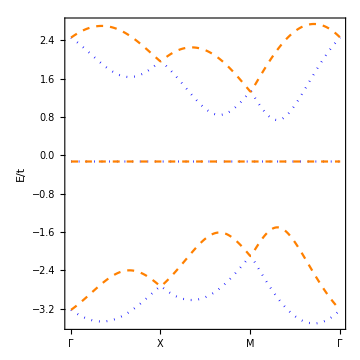

```mathematica
Block[ {λ={0.6,0.0},δ={0.0,0.0},ϵ=0.6,U=0.5, fil=3.0, β=100,krange=25},ListPlot[Table[ PlotMFDisp[λ,δ,ϵ,U,fil,β,krange][[All,i]],{i,1,6,1}],PlotStyle->{{Blue,Dotted},{Orange,Dashed}},
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean-Field Magnetization

```mathematica
Clear[Magn];Magn[λ_,δ_,ϵ_,U_, fil_,β_,krange_,orb_]:= Magn[λ,δ,ϵ,U,fil,β,krange,orb]=  Module[{itr=ItrFnMF[λ,δ,ϵ,U,fil,β,krange]},{1/2( itr[[4,orb]] + itr[[5,orb]]),1/(2I)( itr[[4,orb]] - itr[[5,orb]]), 1/2( itr[[2,orb]] - itr[[3,orb]])}];
```

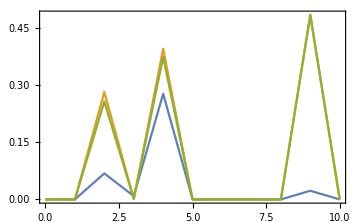

```mathematica
Block[ {λ={0.3,0.0},δ={0.0,0.0}, ϵ=0.6,fil=3, β=100,krange=30},DiscretePlot[{Norm[ Magn[λ,δ,ϵ,U,fil,β,krange,1]],Norm[ Magn[λ,δ,ϵ,U,fil,β,krange,2]],Norm[ Magn[λ,δ,ϵ,U,fil,β,krange,3]]},{U,0,10},PlotRange->All]]
```

```mathematica
?Magn
```

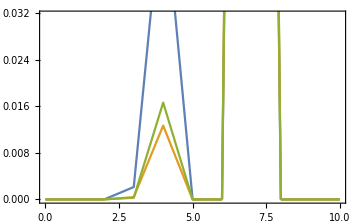

```mathematica
Block[ {λ={0.5,0.0},δ={0.0,0.0}, fil=3, β=100,krange=25},DiscretePlot[{Norm[ Magn[λ,δ,U,fil,β,krange,1]],Norm[ Magn[λ,δ,U,fil,β,krange,2]],Norm[ Magn[λ,δ,U,fil,β,krange,3]]},{U,0,10}]]
```

### Analytic Flat-band Wavefunction

```mathematica
mat2 = {{0,0,a, b, x,y},{0,0,bc, ac,yc,xc},{Conjugate[a],Conjugate[bc],0,0,0,0},{Conjugate[b],Conjugate[ac],0,0,0,0},{Conjugate[x],Conjugate[yc],0,0,0,0},{Conjugate[y],Conjugate[xc],0,0,0,0}};
```

```mathematica
Clear[waveF];waveF[λ_,δ_,k_] := waveF[λ,δ,k]=Normalize[ Module[{a =hamLieb[λ,δ,k] [[1,3]],b=hamLieb[λ,δ,k] [[1,4]],x =hamLieb[λ,δ,k] [[1,5]],y=hamLieb[λ,δ,k] [[1,6]]}, { 0,0,- Conjugate[b] x -  Conjugate[a] y,   - Conjugate[a] x +  Conjugate[b] y, 0,Conjugate[b]^2+ Conjugate[a]^2}]];
```

```mathematica
Clear[waveF2];waveF2[λ_,δ_,k_] := waveF2[λ,δ,k]=Normalize[ Module[{a =hamLieb[λ,δ,k] [[1,3]],b=hamLieb[λ,δ,k] [[1,4]],x =hamLieb[λ,δ,k] [[1,5]],y=hamLieb[λ,δ,k] [[1,6]]}, { 0,-x^2+y^2, 0,0,- x Conjugate[b] -  y Conjugate[a],  y Conjugate[b]+ x Conjugate[a] }]];
```

```mathematica
Block[ {λ=RandomReal[{0,1},2],δ=RandomReal[1,2],k=RandomReal[2π,2]}, hamLieb[λ,δ,k].waveF[λ,δ,k]]//MatrixForm//Chop
```

(0.169958-1.82003 ⅈ
0.214155-1.78597 ⅈ
0
0
0
0)

```mathematica
Block[ {λ=RandomReal[],δ=RandomReal[1,2],k=RandomReal[2π,2]}, hamLieb[λ,δ,k].waveF2[λ,δ,k]]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
Block[ {λ=0.6,δ={0.5,0.0},k=RandomReal[2π,2]}, hamLieb[λ,δ,k].(Normalize[waveF[λ,δ,k]+waveF2[λ,δ,k]])]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
TRO = KroneckerProduct[  IdentityMatrix[3],I  PauliMatrix[2]];
```

```mathematica
Block[ {λ=0.6,δ={0.5,0.0},k=RandomReal[2π,2]}, hamLieb[λ,δ,k].(TRO.Conjugate[Normalize[waveF[λ,δ,-k]+waveF2[λ,δ,-k]]])]//MatrixForm//Chop
```

(0
0
0
0
0
0)

### Wannier Functions

```mathematica
Clear[Psi];Psi[λ_,δ_,k_,band_]:= Psi[λ,δ,k,band]=Module[ {vec =Normalize[waveF[λ,δ,k]+ waveF2[λ,δ,k]], veck =Normalize[waveF[λ,δ,-k]+ waveF2[λ,δ,-k]]},  If[band==1, vec,TRO.Conjugate[veck] ]];
```

```mathematica
Psi[RandomReal[],RandomReal[1,2],RandomReal[2π,2],2]//MatrixForm
```

(-0.52648-0.305972 ⅈ
0.175574+0.0879716 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.626178-0.39227 ⅈ
0.188937+0.0946671 ⅈ)

```mathematica
Clear[WanFuPsi];WanFuPsi[λ_,δ_,r_,krange_,band_] := WanFuPsi[λ,δ,r,krange,band]=1/Length[kSpan[krange]] Sum[Exp[-I k.r]  Psi[λ,δ,k,band] ,{k,kSpan[krange]}]
```

now it’s amplitude

```mathematica
Clear[WFAmpPsi];WFAmpPsi[λ_,δ_,r_,krange_,band_] := WFAmpPsi[λ,δ,r,krange,band] =  Norm[WanFuPsi[λ,δ,r,krange,band]]^2;
```

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1,r=τB}, WanFuPsi[λ,δ,r,krange,band]]//MatrixForm
```

(0.153645+0.144832 ⅈ
-0.629247+0.0804683 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.144832+0.153645 ⅈ
0.629247+0.0804683 ⅈ)

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1},WFAmpPsi[λ,δ,{0,0},krange,band ]]//MatrixForm
```

0.894021

```mathematica
Clear[OmegaPsi];OmegaPsi[ λ_,δ_,range_,krange_,band_] := OmegaPsi[λ,δ,range,krange,band] =  Sum[ Norm[r]^2 WFAmpPsi[λ,δ,r,krange,band] ,{r,rSpan[range]}]- Norm[Sum[r  WFAmpPsi[λ,δ,r,krange,band] ,{r,rSpan[range]}]]^2;
```

#### Wannier Checks

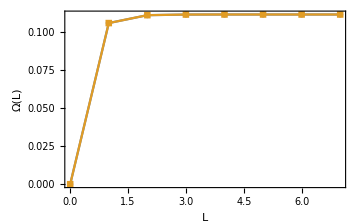

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1},DiscretePlot[ {OmegaPsi[λ,δ,range,krange,1],OmegaPsi[λ,δ,range,krange,2]}, {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic] ]
```

Not much difference between spatial structure of 1 and 2

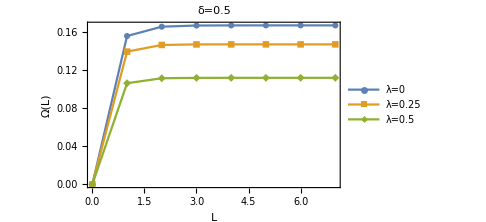

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,band=1},DiscretePlot[ {OmegaPsi[0.0,δ,range,krange,1],OmegaPsi[λ,δ,range,krange,1],OmegaPsi[2 λ,δ,range,krange,1]}, {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic,PlotLegends->{"λ=0","λ=0.25","λ=0.5"},PlotLabel->"δ=0.5"] ]
```

Now let us look at structure of Wannier Function

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,r={0,0},band=1},WanFuPsi[λ,δ,r,krange,band]]//MatrixForm//Chop
```

(0.0915486+0.0834593 ⅈ
-0.643612+0.0244047 ⅈ
0
0
0.0834593+0.0915486 ⅈ
0.643612+0.0244047 ⅈ)

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,r={0,0},band=2},WanFuPsi[λ,δ,r,krange,band]]//MatrixForm//Chop
```

(-0.643612-0.0244047 ⅈ
-0.0915486+0.0834593 ⅈ
0
0
0.643612-0.0244047 ⅈ
-0.0834593+0.0915486 ⅈ)

### Projected Interactions

```mathematica
Clear[ProjIntNN];ProjIntNN[λ_,δ_,r_,l_,krange_,range_]:=ProjIntNN[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]WanFuPsi[λ,δ,-rS,krange,l2][[α]] Conjugate[WanFuPsi[λ,δ,r-rS,krange,l3][[α+1]]]WanFuPsi[λ,δ,r-rS,krange,l4][[α+1]],{α,1,6,2}],{rS,rSpan[range]}]]
```

```mathematica
Clear[ProjIntSF];ProjIntSF[λ_,δ_,r_,l_,krange_,range_]:=ProjIntSF[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]WanFuPsi[λ,δ,-rS,krange,l2][[α+1]] WanFuPsi[λ,δ,r-rS,krange,l3][[α]]Conjugate[WanFuPsi[λ,δ,r-rS,krange,l4][[α+1]]],{α,1,6,2}],{rS,rSpan[range]}]]
```

```mathematica
Clear[ProjIntPH];ProjIntPH[λ_,δ_,r_,l_,krange_,range_]:=ProjIntPH[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]Conjugate[WanFuPsi[λ,δ,-rS,krange,l2][[α+1]] ]WanFuPsi[λ,δ,r-rS,krange,l3][[α+1]]WanFuPsi[λ,δ,r-rS,krange,l4][[α]],{α,1,6,2}],{rS,rSpan[range]}]]
```

#### On-site Hubbard

```mathematica
Block[ {λ=0.0,δ={0.5,0.5}, r={0,0}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 0
1 | 1 | 2 | 1 | 0
1 | 1 | 2 | 2 | 0
1 | 2 | 1 | 1 | 0
1 | 2 | 1 | 2 | 0
1 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 0
2 | 1 | 1 | 1 | 0
2 | 1 | 1 | 2 | 0
2 | 1 | 2 | 1 | 0
2 | 1 | 2 | 2 | 0
2 | 2 | 1 | 1 | 0.361899
2 | 2 | 1 | 2 | 0
2 | 2 | 2 | 1 | 0
2 | 2 | 2 | 2 | 0)

#### Nearest Neighbor

```mathematica
λ=0.2;
```

```mathematica
Block[ {δ={0.5,0.5}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.00074975
1 | 1 | 1 | 2 | 0.0000282629+0.0000810675 ⅈ
1 | 1 | 2 | 1 | 0.0000282629-0.0000810675 ⅈ
1 | 1 | 2 | 2 | 0.0000350069
1 | 2 | 1 | 1 | -0.00202223+0.00146729 ⅈ
1 | 2 | 1 | 2 | -0.000475823+0.0000687614 ⅈ
1 | 2 | 2 | 1 | -0.00014371+0.000487966 ⅈ
1 | 2 | 2 | 2 | 0.0000152577-0.0000406503 ⅈ
2 | 1 | 1 | 1 | -0.00202223-0.00146729 ⅈ
2 | 1 | 1 | 2 | -0.00014371-0.000487966 ⅈ
2 | 1 | 2 | 1 | -0.000475823-0.0000687614 ⅈ
2 | 1 | 2 | 2 | 0.0000152577+0.0000406503 ⅈ
2 | 2 | 1 | 1 | 0.027912
2 | 2 | 1 | 2 | 0.00204922+0.00233598 ⅈ
2 | 2 | 2 | 1 | 0.00204922-0.00233598 ⅈ
2 | 2 | 2 | 2 | 0.001347)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000836984
1 | 1 | 1 | 2 | -7.0433×10^-6+0.0000467884 ⅈ
1 | 1 | 2 | 1 | -7.0433×10^-6-0.0000467884 ⅈ
1 | 1 | 2 | 2 | 0.0000217922
1 | 2 | 1 | 1 | -0.00140838+0.000248645 ⅈ
1 | 2 | 1 | 2 | -0.000240876+0.00016821 ⅈ
1 | 2 | 2 | 1 | -0.000165389+0.000343656 ⅈ
1 | 2 | 2 | 2 | 0.0000595931-0.000118942 ⅈ
2 | 1 | 1 | 1 | -0.00140838-0.000248645 ⅈ
2 | 1 | 1 | 2 | -0.000165389-0.000343656 ⅈ
2 | 1 | 2 | 1 | -0.000240876-0.00016821 ⅈ
2 | 1 | 2 | 2 | 0.0000595931+0.000118942 ⅈ
2 | 2 | 1 | 1 | 0.056911
2 | 2 | 1 | 2 | 0.00103363+0.00217027 ⅈ
2 | 2 | 2 | 1 | 0.00103363-0.00217027 ⅈ
2 | 2 | 2 | 2 | 0.00166441)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntSF[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000164701-0.000350599 ⅈ
1 | 1 | 1 | 2 | 0.0000691506-0.000110677 ⅈ
1 | 1 | 2 | 1 | -0.00125397+0.000381816 ⅈ
1 | 1 | 2 | 2 | -0.000164701+0.000350599 ⅈ
1 | 2 | 1 | 1 | -0.0000321467+0.0000187838 ⅈ
1 | 2 | 1 | 2 | 6.64395×10^-6+0.0000132593 ⅈ
1 | 2 | 2 | 1 | 0.000252444+0.000755318 ⅈ
1 | 2 | 2 | 2 | 0.0000321467-0.0000187838 ⅈ
2 | 1 | 1 | 1 | -0.00080641+0.00228371 ⅈ
2 | 1 | 1 | 2 | 0.00130328+0.000508249 ⅈ
2 | 1 | 2 | 1 | 0.0568661-0.00120367 ⅈ
2 | 1 | 2 | 2 | 0.00080641-0.00228371 ⅈ
2 | 2 | 1 | 1 | -0.000164701+0.000350599 ⅈ
2 | 2 | 1 | 2 | -0.0000691506+0.000110677 ⅈ
2 | 2 | 2 | 1 | 0.00125397-0.000381816 ⅈ
2 | 2 | 2 | 2 | 0.000164701-0.000350599 ⅈ)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntPH[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000165389-0.000343656 ⅈ
1 | 1 | 1 | 2 | -0.00140838+0.000248645 ⅈ
1 | 1 | 2 | 1 | -0.0000595931+0.000118942 ⅈ
1 | 1 | 2 | 2 | -0.000240876+0.00016821 ⅈ
1 | 2 | 1 | 1 | -7.0433×10^-6-0.0000467884 ⅈ
1 | 2 | 1 | 2 | -0.000836984
1 | 2 | 2 | 1 | 0.0000217922
1 | 2 | 2 | 2 | 7.0433×10^-6-0.0000467884 ⅈ
2 | 1 | 1 | 1 | -0.00103363+0.00217027 ⅈ
2 | 1 | 1 | 2 | 0.056911
2 | 1 | 2 | 1 | -0.00166441
2 | 1 | 2 | 2 | 0.00103363+0.00217027 ⅈ
2 | 2 | 1 | 1 | -0.000240876-0.00016821 ⅈ
2 | 2 | 1 | 2 | 0.00140838+0.000248645 ⅈ
2 | 2 | 2 | 1 | 0.0000595931+0.000118942 ⅈ
2 | 2 | 2 | 2 | 0.000165389+0.000343656 ⅈ)

#### Fermionic det

```mathematica
FDet[l_]:= Det[ {{l[[1]], l[[2]], l[[3]], l[[4]]},{l[[2]], l[[3]], l[[4]], l[[1]]},{l[[3]], l[[4]], l[[1]], l[[2]]},{l[[4]], l[[1]], l[[2]], l[[3]]}}];
```

```mathematica
Flatten[Table[ {l1,l2,l3,l4,Sign[FDet[{l1,l2,l3,l4}]]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 1
1 | 1 | 2 | 1 | -1
1 | 1 | 2 | 2 | 0
1 | 2 | 1 | 1 | 1
1 | 2 | 1 | 2 | 0
1 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 1
2 | 1 | 1 | 1 | -1
2 | 1 | 1 | 2 | 0
2 | 1 | 2 | 1 | 0
2 | 1 | 2 | 2 | -1
2 | 2 | 1 | 1 | 0
2 | 2 | 1 | 2 | 1
2 | 2 | 2 | 1 | -1
2 | 2 | 2 | 2 | 0)

#### Detail layout

Density-Density channel

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={1,0}, krange=50,range=3}, {ProjIntNN[λ,δ,r,{1,1,1,1},krange,range],ProjIntNN[λ,δ,r,{2,2,2,2},krange,range],ProjIntNN[λ,δ,r,{1,1,2,2},krange,range],ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]}]//MatrixForm//Chop
```

(0.00074975
0.001347
0.0000350069
0.027912)

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={-1,0}, krange=50,range=3}, {ProjIntNN[λ,δ,r,{1,1,1,1},krange,range],ProjIntNN[λ,δ,r,{2,2,2,2},krange,range],ProjIntNN[λ,δ,r,{1,1,2,2},krange,range],ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]}]//MatrixForm//Chop
```

(0.001347
0.00074975
0.0000350069
0.027912)

Spin flip-Spin flip channel

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={-1,0}, krange=50,range=3}, {ProjIntSF[λ,δ,r,{1,2,1,2},krange,range],ProjIntSF[λ,δ,r,{1,2,2,1},krange,range],ProjIntSF[λ,δ,r,{2,1,1,2},krange,range],ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]}]//MatrixForm//Chop
```

(-8.84664×10^-6+0.000018777 ⅈ
-0.000802558-0.000497146 ⅈ
-6.1693×10^-6-0.000737043 ⅈ
0.0277186-0.00200912 ⅈ)

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={1,0}, krange=50,range=3}, {ProjIntSF[λ,δ,r,{1,2,1,2},krange,range],ProjIntSF[λ,δ,r,{1,2,2,1},krange,range],ProjIntSF[λ,δ,r,{2,1,1,2},krange,range],ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]}]//MatrixForm//Chop
```

(-8.84664×10^-6-0.000018777 ⅈ
-6.1693×10^-6+0.000737043 ⅈ
-0.000802558+0.000497146 ⅈ
0.0277186+0.00200912 ⅈ)

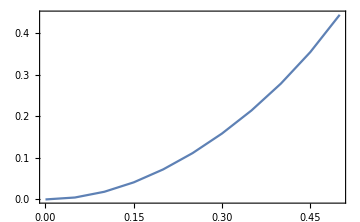

```mathematica
Block[ {δ={0.5,0.5}, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]-ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{λ,0.,0.5,0.05},PlotLegends->Automatic]]
```

```mathematica
Block[ {λ=0.0,δ=0.5, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{1,0},{2,1,2,1},krange,range]-ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{0,1},{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{θ,0.,2π,0.1},PlotLegends->Automatic]]
```

$Aborted

```mathematica
Block[ {λ=0.2,δ=0.5, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{1,0},{2,1,2,1},krange,range]-ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{0,1},{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{θ,0.,2π,0.1},PlotLegends->Automatic]]
```